```mathematica
dir080916C="/Users/maxitg/Projects/GammaRays/GRObservations/DerivedData/GRObservations/Build/Products/Release/080916C/";
```

```mathematica
dir090510="/Users/maxitg/Projects/GammaRays/GRObservations/DerivedData/GRObservations/Build/Products/Release/090510/";
```

```mathematica
dir090902B="/Users/maxitg/Projects/GammaRays/GRObservations/DerivedData/GRObservations/Build/Products/Release/090902B/";
```

```mathematica
dir090926A="/Users/maxitg/Projects/GammaRays/GRObservations/DerivedData/GRObservations/Build/Products/Release/090926A/";
```

```mathematica
bursts={dir080916C,dir090510,dir090902B,dir090926A};
```

```mathematica
ranges={
{-0.05 300,300},
{-0.05 60,60},
{-0.05 1000,1000},
{-0.05 300,300}
};
```

```mathematica
gevData=Table[Import[burst<>"gev","Table"],{burst,bursts}];
```

```mathematica
mevData=Table[Import[burst<>"mev","Table"],{burst,bursts}];
```

```mathematica
probData=Table[Import[burst<>"probs","Table"]/.{κ_,p_,a_,b_,c_}->{κ,p},{burst,bursts}];
```

#### Presentation

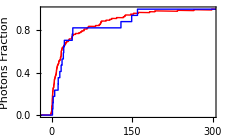
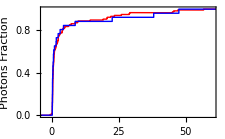
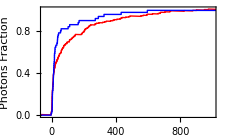
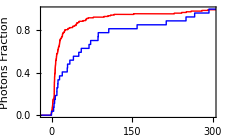

```mathematica
Table[ListPlot[{mevData[[i]],gevData[[i]]},Joined->True,PlotRange->{ranges[[i]],All},PlotStyle->{{Thick,Red},{Thick,Blue}},Frame->{{True,False},{True,False}},FrameLabel->{"Time, sec","Photons Fraction"},PlotLegends->Placed[{Style["100 MeV - 1 GeV",Red],Style["1 GeV - 300 GeV",Blue]},{0.7,0.25}],ImageSize->225,FrameStyle->Gray],{i,1,Length[mevData]}]
```

#### Paper

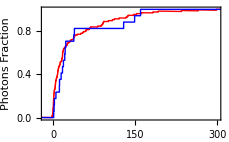
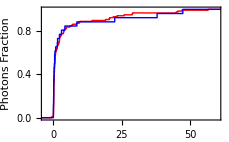
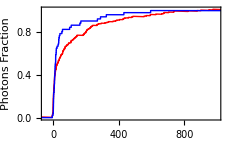
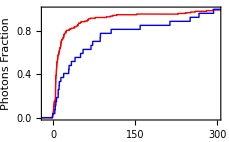

```mathematica
Table[ListPlot[{mevData[[i]],gevData[[i]]},Joined->True,PlotRange->{ranges[[i]],All},PlotStyle->{Red,Blue},Frame->{{True,False},{True,False}},FrameLabel->{"Time, sec","Photons Fraction"},PlotLegends->Placed[{Style["100 MeV - 1 GeV",FontSize->10],Style["1 GeV - 300 GeV",FontSize->10]},{0.7,0.25}],ImageSize->230.1799598,FrameStyle->Directive[FontSize->10]],{i,1,Length[mevData]}]
```

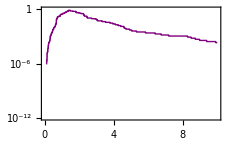
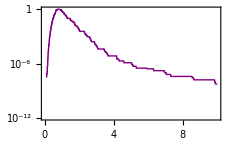
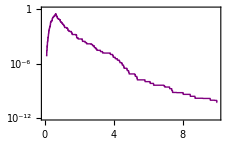
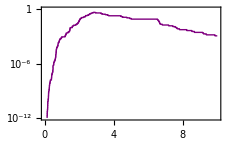

```mathematica
Table[Show[
ListLogPlot[probData[[i]],Joined->True,PlotRange->{{0,10},{1.*^-12,1.}},PlotStyle->RGBColor[0.5,0,0.5],Frame->{{True,False},{True,False}},FrameLabel->{"Stretching Factor","KS Probability"},ImageSize->230.1799598,FrameStyle->Directive[FontSize->10]](*,
LogPlot[Table[1-Erf[σ/(√2)],{σ,1,7}],{κ,0,10},PlotStyle->{Thin,Gray}]*)
],{i,1,Length[probData]}]
```

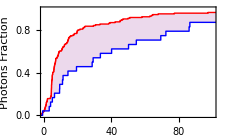

```mathematica
ListPlot[{mevData,gevData},Joined->True,PlotRange->{{0,100},{0,1}},PlotStyle->{{Thick,Red},{Thick,Blue}},Frame->{{True,False},{True,False}},FrameLabel->{"Time, sec","Photons Fraction"},PlotLegends->Placed[{Style["100 MeV - 1 GeV",Red],Style["1 GeV - 300 GeV",Blue]},{0.7,0.25}],Filling->{1->{2}},FillingStyle->RGBColor[0.5,0,0.5,0.15],ImageSize->225,FrameStyle->Gray]
```

```mathematica
probsData[[3256]][[5]]-probsData[[3256]][[4]]
```

0.174099

```mathematica
arrow[time_,gev_,mev_,headSize_]:=Graphics[{Arrowheads[{-headSize,headSize}],Arrow[{{time,gev},{time,mev}}]}];
```

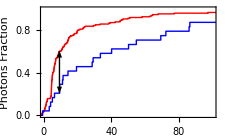

```mathematica
Show[ListPlot[{mevData,gevData},Joined->True,PlotRange->{{0,100},{0,1}},PlotStyle->{{Thick,Red},{Thick,Blue}},Frame->{{True,False},{True,False}},FrameLabel->{"Time, sec","Photons Fraction"},FrameStyle->Gray,PlotLegends->Placed[{Style["100 MeV - 1 GeV",Red],Style["1 GeV - 300 GeV",Blue]},{0.7,0.25}]],arrow[probsData[[2305]][[3]],probsData[[2305]][[4]],probsData[[2305]][[5]],0.08],ImageSize->225]
```

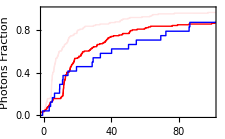

```mathematica
ListPlot[{mevData,mevData/.{time_,value_}->{2.58775time,value},gevData},Joined->True,PlotRange->{{0,100},{0,1}},PlotStyle->{{Thick,RGBColor[1,0,0,0.1]},{Thick,Red},{Thick,Blue}},Frame->{{True,False},{True,False}},FrameLabel->{"Time, sec","Photons Fraction"},FrameStyle->Gray,PlotLegends->Placed[{None,Style["100 MeV - 1 GeV",Red],Style["1 GeV - 300 GeV",Blue]},{0.7,0.25}],ImageSize->225]
```

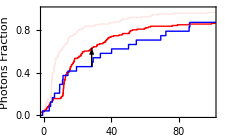

```mathematica
Show[ListPlot[{mevData,mevData/.{time_,value_}->{2.58775time,value},gevData},Joined->True,PlotRange->{{0,100},{0,1}},PlotStyle->{{Thick,RGBColor[1,0,0,0.1]},{Thick,Red},{Thick,Blue}},Frame->{{True,False},{True,False}},FrameLabel->{"Time, sec","Photons Fraction"},FrameStyle->Gray,PlotLegends->Placed[{None,Style["100 MeV - 1 GeV",Red],Style["1 GeV - 300 GeV",Blue]},{0.7,0.25}]],arrow[2.58775probsData[[3256]][[3]],probsData[[3256]][[4]],probsData[[3256]][[5]],-0.08],ImageSize->225]
```

```mathematica
probsData[[3256]]
```

{2.58775,0.51911,10.9484,0.458333,0.632432}

```mathematica
Sort[probsData,#1[[2]]>#2[[2]]&]
```

{{2.58775,0.51911,10.9484,0.458333,0.632432},{2.58516,0.51911,10.9484,0.458333,0.632432},{2.58258,0.51911,10.9484,0.458333,0.632432},{2.58,0.51911,10.9484,0.458333,0.632432},{2.57742,0.51911,10.9484,0.458333,0.632432},«4598»,{0.100401,5.97014×10^-13,30.593,0.0416667,0.852334},{0.1003,5.97014×10^-13,30.593,0.0416667,0.852334},{0.1002,5.97014×10^-13,30.593,0.0416667,0.852334},{0.1001,5.97014×10^-13,30.593,0.0416667,0.852334},{0.1,5.97014×10^-13,30.593,0.0416667,0.852334}}